```mathematica
Manipulate[
Module[{ρ,MW,R,Cp,γ,d1,T1,P2,sol,u2,T2,P1},
ρ[T_]:=P2/(8.314*^-3/MW*T);(*kg/m3*)
MW=0.02897;(*kg/mol*)
R=8.314;
Cp=5/2*R/MW;(*J/kg/K*)
γ=1.4;

d1=0.06;(*m*)
T1=400;(*K*)
P2=101.3;(*kPa*)

sol=Quiet@Last@Solve[u1*d1^2*ρ[T1]==u*d2^2*ρ[t]∧Cp*(t-T1)==1/2*(u1^2-u^2),{u,t},Reals];
u2=u/.sol;
T2=t/.sol;
P1=P2*(T2/T1)^(-γ/(γ-1));

Text@Style[Row[{
Grid[{{"u_1 =",u1,"m/s"},{"T_1 =",T1,"K"},{"P_1 =",P1,"kPa"}}],
Spacer[50],
Grid[{{"u_2 =",u2,"m/s"},{"T_2 =",T2,"K"},{"P_2 =",P2,"kPa"}}]
}],17]
],
Control[{{u1,32,"inlet velocity (m/s)"},10,150,1,Appearance->"Labeled"}],
Control[{{d2,0.03,"outlet diameter (m)"},0.02,0.10,0.01,Appearance->"Labeled"}]
]
```

u_1 π/4 d_1^2 ρ_1=u_2 π/4 d_2^2 ρ_2

Cp T_1+u_1^2/2=Cp T_2 u_2^2/2

Ideal gas heat capacity: Cp=5 R/2

where u_i is velocity, m_i is mass flow rate, d_i is diameter, ρ is air density, Cp is heat capacity, T_i is temperature, and R is the gas constant.

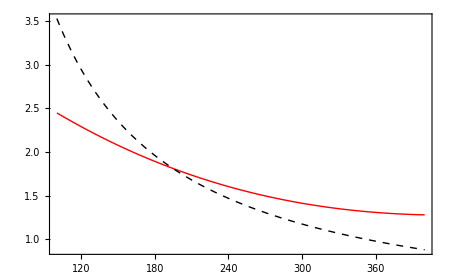

```mathematica
Module[{P2,MW,ρ1,ρ2},
P2=101.3;
MW=0.02897;

ρ1[T_]:=-9*^-9*T^3+2*^-5*T^2-0.012*T+3.4578;
ρ2[T_]:=P2/(8.314*^-3/MW*T);

Plot[{ρ1[T],ρ2[T]},{T,100,400},PlotStyle->{{Thick,Red},{Thick,Dashed,Black}},Frame->True,ImageSize->450]
]
```